## 1. Curves

## 1.1 Curves defined explicitly

If you recall, single-variable calculus involved explicit functions of a single variable, e.g. y = t^2, y=sin(t), or more generally y = f(t). You spent a lot of time visualizing these functions, solving equations with these functions, and computing related properties like derivatives and integrals.  

An explicit function, y = f(t), is straight-forward to visualize in Mathematica. Let’s consider the exponential function, y = e^t, for t between -1 and 1. To get started, here is an example of the Plot function:

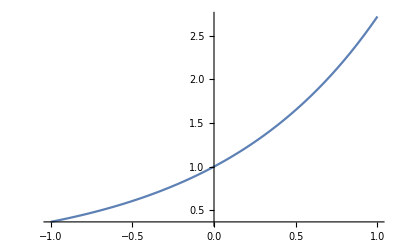

```mathematica
Plot[Exp[t],{t,-1,1}]
```

The first argument is the function, and the second argument is the domain. Note that in Mathematica every built-in function begins with a capital letter, and the argument to the function is enclosed in square brackets [ ]. There are some simple options to make the plot look better:

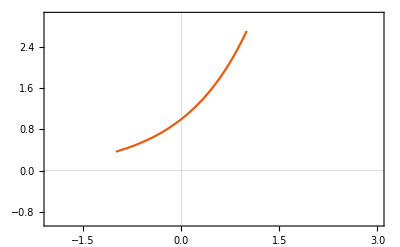

```mathematica
Plot[Exp[t], {t,-1,1},PlotRange->{{-2,3},{-1,3}}, PlotTheme->"Scientific"]
```

Here we have used the PlotRange option to set the minimum and maximum x- and y-values - this only changes the axes, not the domain over which the function is defined.  We also used the PlotTheme option to set a particular type of theme so that the graphic looks “scientific”. The arrow after options like PlotRange and PlotTheme is defined by typing ->.

The power of Mathematica becomes apparent when we consider the more general exponential function, y = A e^kt. It is straight-forward to use Manipulate to visualize this function for different values of the parameters A and k:

```mathematica
Manipulate[Plot[A*Exp[k*t], {t,-1,1},PlotRange->{{-2,2},{-4,4}}, PlotTheme->"Scientific"],{A,1,2,Appearance->"Labeled"},{k,-10,10,Appearance->"Labeled"}]
```

Notice how we have embedded or nested our previous Plot function inside the Manipulate function. We’ve included two parameters in the definition of our exponential function, and provided a range for each of these. Manipulate generates a figure with sliders for each of the parameters - the Appearance option labels the slider so that we know the current value of each parameter.

Varying the parameters in this way allows us to explore how the curve changes. Here we see that the parameter A controls the point at which the curve crosses the y-axis, while the parameter k controls the "type" and "strength" of the exponential. Positive values of k define increasing exponentials, larger values leading to more rapidly increasing curves. Negative values of k define decreasing exponentials.

The limiting behavior of functions is often important, and Mathematica makes it straight-forward to evaluate limiting behavior using the Limit function. For example, we know that the exponential function keeps increasing for positive k as we increase t. Likewise, we expect that the exponential function tends to zero as we decrease t. Both of these limits can be evaluated as follows:

```mathematica
Limit[Exp[k*t],t->∞]
Limit[Exp[k*t],t->-∞]
```

ConditionalExpression[∞,k>0]

ConditionalExpression[0,k>0]

The first argument is the function, and the second argument is the point we wish to approach. To get “infinity”, you can either use the writing assistant and choose infinity from the typeset menu, or you can use “EscinfEsc”. These limits return conditional answers that are consistent with our expectations.

The meaning and interpretation of parameters and curves depends on their application. For example, the exponential function is often used in models of population growth where t is time. In this context, the parameter A is the initial population at t = 0 and the parameter k is the growth rate (k > 0) or decay rate (k < 0).  A population that is growing exponentially at 1% per year has k = 0.01.

In popular media, anything that grows rapidly is often termed as growing "exponentially". However, exponential growth is a very special type of growth in the following sense: the time that it takes a population to double is independent of the population size. To confirm this, let's find out how long it takes for a population of size A to double to 2A. We can use the Solve function to do this:

```mathematica
Solve[A*Exp[k*t]==2*A,t,Reals]
```

{{t→Log[2]/k}}

The first argument to Solve is the equation to be solved, the second argument is the variable to solve for, and the third argument Reals is an option that directs Solve to assume that the variables and parameters in the equations are all real. Notice that the solution depends on the growth rate k, but it is independent of the initial population size A. 

Notice that the equation used inside the Solve function uses == instead =. You can think of = as a definition and == as an equality. In everyday mathematics language we often use these interchangeably, with the meaning depending on the circumstance. This sort of ambiguity is not good for a computer algebra system. Go ahead and edit the last input and use a single = instead of a double ==.  You will get an error message that is hard to fathom!

Although we have determined a general solution for all parameter values, we are often interested in specific solutions, e.g. k = 0.01. It’s worth taking a moment to learn how to evaluate a general solution with specific parameter values. Here is one approach that values clarity of expression over brevity:

```mathematica
gensol = Solve[A*Exp[k*t]==2*A,t, Reals]
specsol=gensol/.{k->1/100}
N[specsol]
```

{{t→Log[2]/k}}

{{t→100 Log[2]}}

{{t→69.3147}}

A population that is growing exponentially at 1% per year takes just over 69 years to double. If this growth rate doesn’t change, then it will take another 69 years for it to double again, and so on.

There are number of Mathematica things to note here. First, we assign the result of the Solve function to a variable named gensol, which I’m using as short-hand for general solution. You can call this anything you like, but it’s good practise to use a variable name that is meaningful to you. Second, I’m evaluating gensol at specific values of the parameters using the /. notation, and each of the parameters are mapped to specific values using the -> notation. The result, which is still exact, is stored in the variable specsol. Third, I produce a numerical approximation to the specific solution using the N function. Finally, note that in each case the solution is returned as a list of rules - we will have more to say about this in the future.

Although I don’t recommend it if you are starting out, the reality is that nested functions work beautifully in Mathematica, and most experienced users don’t use temporary variables to keep track of their work - rather they wrap each function as soon as they have tested it. For example, an intermediate user might develop the lines above as follows, where % refers to the most recent output:

```mathematica
Solve[A*Exp[k*t]==2*A,t, Reals]
%/.{k->1/100}
N[%]
```

{{t→Log[2]/k}}

{{t→100 Log[2]}}

{{t→69.3147}}

An experienced user on the other hand will simply nest the functions as they go:

```mathematica
N[Solve[A*Exp[k*t]==2*A,t, Reals]/.{k->1/100}]
```

{{t→69.3147}}

While this is very cute, it makes debugging very difficult indeed! I highly recommend that you stay away from this approach unless you are very experienced.

## Exercises

Use Plot and Manipulate to visualize the function y = m x + b for different values of m and b. What features of the curve do m and b control? Use Solve to find the general value(s) of x corresponding to y = 3 and the specific value(s) of x for m = 4, b = 1?

This is a warm-up question.You should recognize this as the equation for a straight-line and the meaning of the parameters m and b should be familiar. The main challenge here is to think through the set of values for m and b, and a domain for x that makes visualizing meaningful. You should check the general solution by working it out on a piece of paper.

```mathematica
Manipulate[Plot[m*x+b, {x,-10, 10}], {m,1,2,Appearance->"Labeled"},{b,-10,10,Appearance->"Labeled"}]
```

```mathematica
Clear[m,b]
Solve[m*x+b==3, x, Reals]
```

{{x→(3-b)/m}}

```mathematica
Solve[4*x+1==3, x]
```

{{x→1/2}}

Use Plot and Manipulate to visualize the logistic function y =  L/(1 + e^(-k(x-x_0))) for different values of L > 0, k>0, x_0.  Use Limit to explore the limiting behavior of the function for large positive and negative x, and use Solve to find the general value(s) of x corresponding to y = L/2. What features of the curve do A,k, x_0 control? What is the interpretation of the parameters in terms of population growth?

This form of the logistic function arises in studies of population growth - see the Wikipedia article on the logistic function for some background and help in interpreting the parameters. Finding the value of x that corresponds to y=L/2 will help with your interpretation of the parameters.

```mathematica
ClearAll
Manipulate[Plot[L/(1+E^(-k(x-x0))), {x, -10, 10}], {L,0,10,Appearance->"Labeled"},{k,0,1,Appearance->"Labeled"}, {x0,0,10,Appearance->"Labeled"}]
```

ClearAll

L controls the overall height of the function. k controls the function’s growth rate. x0 controls the horizontal position of the graph. In terms of population, L is the carrying capacity of the environment, k is the population’s growth rate, and x0 is dependent on the time at which the population starts growing.

```mathematica
Solve[L/(1+E^-k(x-x0))==L/2, Reals]
```

{{x→ⅇ^2}}

Use Plot and Manipulate to visualize the power function y = a x^n+ b with x between 0 and 1, for different values of the parameters n ≥ 0, a, b. What features of the curve does n, a, b control? Describe the curve as n →∞.

This question involves a power function which we will use when studying the shape of a boat.

```mathematica
Manipulate[Plot[a*x^n+b, {x, 0,1}], {n,0,10,Appearance->"Labeled"}, {a,-10,10,Appearance->"Labeled"}, {b,-10,10,Appearance->"Labeled"}]
```

N represents the concavity of the curve, a controls the height and whether the curve is on the top or bottom of the x axis, and b controls the height of the curve.

```mathematica
Limit[a*x^n+b, n->∞]
```

ConditionalExpression[∞,b∈ℝ&&a>0&&Log[x]>0]

Use Plot and Manipulate to visualize the trigonometric function y = A sin(ω t + ϕ) for different values of A , ω, and ϕ. What features of the curve do A, ω, and ϕ control? Use the internet to deepen your understanding of these parameters. Use Solve to find the general value(s) of t corresponding to y = 2 and the specific value(s) of t for A = 3,  ω= 4, ϕ = 5?

This question contains three parameters and involves a trigonometric function and form that is common in engineering - check out the Wikipedia article on simple harmonic motion. The general and specific solutions are no longer unique, and some of the terminology in the solution require interpretation.

```mathematica
Manipulate[Plot[A*Sin[(ωt+ϕ)], {t, -6,6}], {A,-5,5,Appearance->"Labeled"}, {ω,-1,1,Appearance->"Labeled"}, {ϕ,-1,1,Appearance->"Labeled"}]
```

```mathematica
Clear[A,ω, ϕ]
Solve[A*Sin[(ωt+ϕ)]== 2, Reals]
```

{{ω→ConditionalExpression[-(ϕ-ArcSin[2/A]-2 π C[1])/t,(C[1]∈ℤ&&A≥2)||(C[1]∈ℤ&&A≤-2)]},{ω→ConditionalExpression[-(-π+ϕ+ArcSin[2/A]-2 π C[1])/t,(C[1]∈ℤ&&A≥2)||(C[1]∈ℤ&&A≤-2)]},{t→ConditionalExpression[0,(C[1]∈ℤ&&A≥2)||(C[1]∈ℤ&&A≤-2)],ϕ→ConditionalExpression[π-ArcSin[2/A]+2 π C[1],(C[1]∈ℤ&&A≥2)||(C[1]∈ℤ&&A≤-2)]},{t→ConditionalExpression[0,(C[1]∈ℤ&&A≥2)||(C[1]∈ℤ&&A≤-2)],ϕ→ConditionalExpression[ArcSin[2/A]+2 π C[1],(C[1]∈ℤ&&A≥2)||(C[1]∈ℤ&&A≤-2)]}}

```mathematica
A = 3
ω = 4
ϕ = 5
Solve[A*Sin[(ωt+ϕ)]== 2, Reals]
```

3

4

5

{{t→ConditionalExpression[-5/4+1/4 (π-ArcSin[2/3]+2 π C[1]),C[1]∈ℤ]},{t→ConditionalExpression[-5/4+1/4 (ArcSin[2/3]+2 π C[1]),C[1]∈ℤ]}}

Use Plot and Manipulate to visualize the quadratic polynomial in vertex form y = (g(x-h))^2+k, for different values of g,h,and k. What features of the curve do g, h, and k control? What is the relationship between g,h, and k in the vertex form and a, b, and c in the standard form y = c + b x + a x^2? (This will require a little algebra.) 

The quadratic polynomial is probably very familiar to you. There are numerous ways to write this second-order polynomial, and we’ve used two forms here: the standard form and the vertex form. Using Plot and Manipulate on the standard form is possible, but it would be hard to tell the effect of each parameter. Using the vertex form, however, the effect of each parameter is much easier to interpret.

```mathematica
Manipulate[Plot[(g(x-h)^2)+k , {x, -10,10}], {g,-5,5,Appearance->"Labeled"}, {h,-10,10,Appearance->"Labeled"}, {k,-10,10,Appearance->"Labeled"}]
```

g controls the concavity of the parabola, h and k control the coordinates of the parabola’s vertex. In ax^2+bx+c form, a = g, b=2gh, and c=gh^2+k.

## 1.2 Curves defined implicitly

Not every curve can be expressed in terms of an explicit function in which there is only one output for each value of the input. Curves can also be expressed implicitly through a relationship between 2 variables. A circle is a good example. For example, the equation for a circle of radius 1, centered at the origin, is x^2+y^2-1 = 0. The left-hand side of this equation can be thought of as a function of two variables, f(x,y) = x^2+y^2-1 and the set of points (x,y) where f=0 defines a curve that we like to call the unit circle. In Mathematica, we visualize implicit functions using the ContourPlot function:

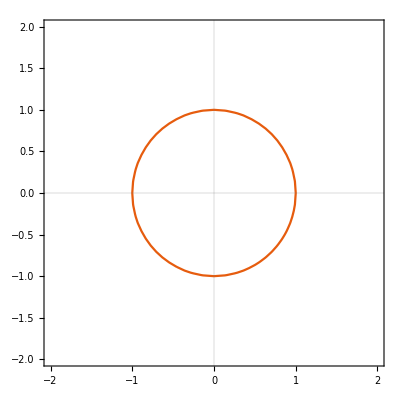

```mathematica
ContourPlot[x^2+y^2 - 1 == 0,{x,-2,2},{y,-2,2},PlotTheme->"Scientific"]
```

The first argument is the equation that we wish to visualize, and the next two arguments define the domain for the visualization. 

Now assume we wish to visualize the equation for a circle of radius R, centered at the origin, x^2+y^2-R^2=0. It is straightforward to incorporate the Manipulate function as before:

```mathematica
Manipulate[ContourPlot[x^2+y^2 - R^2 == 0,{x,-2,2},{y,-2,2},PlotPoints->50,PlotTheme->"Scientific"],{R,1,2,Appearance->"Labeled"}]
```

Notice that here we have defined a circle of radius R, where R can vary between 1 and 2.

Now that we have more curves at our disposal, we can start to ask some geometrical questions about curves. For example, we could Solve to determine the intersection points of two curves. Consider a circle of radius R centered at the origin, and an arbitrary straight-line. To find possible intersection points, we’d like to solve both equations simultaneously

						x^2+ y^2 = R^2
y = m x + b

where R is the radius of the circle, m is the slope of the line, and b is the y-intercept of the line.

```mathematica
Solve[x^2 + y^2 ==R^2&&y==m*x+b,{x,y}]
```

{{x→(-b m-√(-b^2+R^2+m^2 R^2))/(1+m^2),y→b-(b m^2)/(1+m^2)-(m √(-b^2+R^2+m^2 R^2))/(1+m^2)},{x→(-b m+√(-b^2+R^2+m^2 R^2))/(1+m^2),y→b-(b m^2)/(1+m^2)+(m √(-b^2+R^2+m^2 R^2))/(1+m^2)}}

Notice we use the “&&” operator when we want both equations to be true at the same time, and that we ask Solve to find the unknown pair {x,y}. The solution returned to us looks promising - it has two pairs of solutions which would correspond to two intersection points. These could be complex due to the presence of the square roots and therefore not a valid solution, which also makes sense since the line could miss the circle entirely. We could pass the Reals option to Solve if we wanted to determine the precise conditions for intersection points to exist - go ahead and try it - you will find the relevant conditions on the parameters that guarantee real solutions and therefore the existence of intersection points.

The solution is currently a list of assignments. Since we are going to plot these points next, we first take the step of mapping these assignments to a list of points. One way of doing this is as follows:

```mathematica
gensol = Solve[x^2 + y^2 ==R^2&&y==m*x+b,{x,y}]
points = {x,y}/.gensol
```

{{x→(-b m-√(-b^2+R^2+m^2 R^2))/(1+m^2),y→b-(b m^2)/(1+m^2)-(m √(-b^2+R^2+m^2 R^2))/(1+m^2)},{x→(-b m+√(-b^2+R^2+m^2 R^2))/(1+m^2),y→b-(b m^2)/(1+m^2)+(m √(-b^2+R^2+m^2 R^2))/(1+m^2)}}

{{(-b m-√(-b^2+R^2+m^2 R^2))/(1+m^2),b-(b m^2)/(1+m^2)-(m √(-b^2+R^2+m^2 R^2))/(1+m^2)},{(-b m+√(-b^2+R^2+m^2 R^2))/(1+m^2),b-(b m^2)/(1+m^2)+(m √(-b^2+R^2+m^2 R^2))/(1+m^2)}}

Notice that we’ve defined points as a pair of coordinates obtained by replacing the general solution. As desired, the variable points now contains the solution as a list of (x,y)-coordinates.

As a final example of the power of Manipulate we plot the line, the circle, and intersection points as we vary the parameters. In this formulation we use new parameters RR, mm, and bb. Notice how we have to map the parameters in the intersection points to these new variables. We have to take this step because the parameters in points is only available to the ListPlot function and we need to make them available to the Manipulate function. There are more elegant ways to do this which we will meet in the future. We also use a PlotPoints option which helps to smooth the circle and line, and a PlotStyle option to plot the points in red. Note that we compute the general solution again here so that everything we need is defined within this one cell. We use Show to plot multiple objects at the same time.

```mathematica
gensol = Solve[x^2 + y^2 ==R^2&&y==m*x+b,{x,y}]
points = {x,y}/.gensol
Manipulate[Show[ContourPlot[y==mm*x+bb,{x,-4,4},{y,-4,4},PlotPoints->50],ContourPlot[x^2 + y^2 ==RR^2,{x,-4,4},{y,-4,4},PlotPoints->50],ListPlot[points/.{R->RR,m->mm,b->bb},PlotStyle->Red]],{RR,1,2,Appearance->"Labeled"},{mm,-10,10,Appearance->"Labeled"},{bb,-2,2,Appearance->"Labeled"}]
```

{{x→(-b m-√(-b^2+R^2+m^2 R^2))/(1+m^2),y→b-(b m^2)/(1+m^2)-(m √(-b^2+R^2+m^2 R^2))/(1+m^2)},{x→(-b m+√(-b^2+R^2+m^2 R^2))/(1+m^2),y→b-(b m^2)/(1+m^2)+(m √(-b^2+R^2+m^2 R^2))/(1+m^2)}}

{{(-b m-√(-b^2+R^2+m^2 R^2))/(1+m^2),b-(b m^2)/(1+m^2)-(m √(-b^2+R^2+m^2 R^2))/(1+m^2)},{(-b m+√(-b^2+R^2+m^2 R^2))/(1+m^2),b-(b m^2)/(1+m^2)+(m √(-b^2+R^2+m^2 R^2))/(1+m^2)}}

There is no end to the functions of two variables that you can define. There is, however, a set of functions that show up again and again, and these are the quadratic functions of two variables. The general form (containing all possible quadratic, linear and constant terms) is

a x^2+b x y + c y^2+d x + e y + f = 0

where a, b,c,d,e,and f are arbitrary parameters, some of which may be zero. The curves defined by this equation are called conic sections, and represent the intersection of a double cone and a plane. The non-degenerate cases include circles, parabolas, ellipses, and hyperbolas. See the Wikipedia article on conic section for more information.

## Exercises

Use the internet to find the implicit equation for a circle of radius R, centered at the point (a,b). Use ContourPlot and Manipulate to visualize the circle for different values of a, b, and R.

This is a warm-up question. The implicit equation for a circle centered away from the origin should be easy to find, and you should use the visualization to check that changing the parameters moves the circle and changes its radius in the way you expect.

```mathematica
Manipulate[ContourPlot[(x-a)^2+(y-b)^2 - R^2 == 0,{x,-2,2},{y,-2,2},PlotPoints->50,PlotTheme->"Scientific"],{R,1,2,Appearance->"Labeled"}, {a,-2,2,Appearance->"Labeled"}, {b,-2,2,Appearance->"Labeled"}]
```

Use ContourPlot and Manipulate to visualize the implicit equation for an ellipse x^2/a^2+y^2/b^2-1=0 for different values of a and b. What features of the ellipse do a and b control? Use the internet to deepen your understanding of the parameters a and b - see for example the Wikipedia article on conic section.

This question requires a little modification to the visualization for the circle, and a little internet research to fully understand the parameters. Start with the article on conic section, and then spend a little time exploring after that - don’t get lost in the world of the internet, and don’t be surprised when you see lots of terminology that you don’t understand.

```mathematica
Manipulate[ContourPlot[x^2/a^2+y^2/b^2-1== 0,{x,-2,2},{y,-2,2},PlotPoints->50,PlotTheme->"Scientific"], {a,1,2,Appearance->"Labeled"}, {b,1,2,Appearance->"Labeled"}]
```

a controls the ellipse’s width and b controls the height.

Use ContourPlot and Manipulate to visualize the implicit equation for an hyperbola x^2/a^2-y^2/b^2-1=0 for different values of a > 0 and b > 0. What features of the hyperbola do a and b control? Use the internet to deepen your understanding of the parameters a and b.

This question is similar to the one for the ellipse. In this case, however, interpreting the parameters without some additional reading is much harder because the precise impact of the parameters is not obvious from visualization. Again, start with the Wikipedia article on conic section and take it from there.

```mathematica
Manipulate[ContourPlot[x^2/a^2-y^2/b^2-1== 0,{x,-2,2},{y,-10,10},PlotPoints->50,PlotTheme->"Scientific"], {a,0.1,2,Appearance->"Labeled"}, {b,0.1,2,Appearance->"Labeled"}]
```

A controls the distance from the center that the hyperbola starts and how closely it follows the asymptotes, and b controls the slope of the asymptotes

Use the internet to find the conditions under which the solutions of  

a x^2+b x y + c y^2+d x + e y + f = 0

define an ellipse, a parabola, a hyperbola, and a circle. 

This question is meant to broaden your understanding of  the possible solutions of this general quadratic polynomial in two variables. Start with the Wikipedia article on conic section.

Parabola: ax^2+dx+f-ey=0 where e=0
Hyperbola: a and b would represent 1/a and 1/b since multiplying by a fraction is the same as dividing. (b is negative). You would not need to include b, d, or e, and f= -1
Ellipse:  Same as hyperbola but with a positive b 
Circle: B, D, E = DNE, A=C, F is negative, so x^2+y^2-f=0

Consider an ellipse, centered at the origin, and an arbitrary straight-line. Find the intersection of points of the ellipse with the line, and plot both curves and points as detailed in the earlier example.

This question asks you to bring a number of ideas together at the same time, and it is based on the examples in this section.

```mathematica
Clear[A,B]
gensol = Solve[(x^2)/(A^2)+(y^2)/(B^2)-1==0&&y==m*x+b,{x,y}]
points = {x,y}/.gensol
Manipulate[Show[ContourPlot[y==mm*x+bb,{x,-4,4},{y,-4,4},PlotPoints->50],ContourPlot[(x^2)/(AA^2)+(y^2)/(BB^2)-1==0,{x,-4,4},{y,-4,4},PlotPoints->50],
ListPlot[points/.{A->AA,B->BB, m->mm,b->bb},PlotStyle->Red]],{AA,1,2,Appearance->"Labeled"}, {BB,1,2,Appearance->"Labeled"},{mm,-10,10,Appearance->"Labeled"},{bb,-2,2,Appearance->"Labeled"}]
```

{{x→(-A^2 b m-√(-A^2 b^2 B^2+A^2 B^4+A^4 B^2 m^2))/(B^2+A^2 m^2),y→b-(A^2 b m^2)/(B^2+A^2 m^2)-(m √(-A^2 B^2 (b^2-B^2-A^2 m^2)))/(B^2+A^2 m^2)},{x→(-A^2 b m+√(-A^2 b^2 B^2+A^2 B^4+A^4 B^2 m^2))/(B^2+A^2 m^2),y→b-(A^2 b m^2)/(B^2+A^2 m^2)+(m √(-A^2 B^2 (b^2-B^2-A^2 m^2)))/(B^2+A^2 m^2)}}

{{(-A^2 b m-√(-A^2 b^2 B^2+A^2 B^4+A^4 B^2 m^2))/(B^2+A^2 m^2),b-(A^2 b m^2)/(B^2+A^2 m^2)-(m √(-A^2 B^2 (b^2-B^2-A^2 m^2)))/(B^2+A^2 m^2)},{(-A^2 b m+√(-A^2 b^2 B^2+A^2 B^4+A^4 B^2 m^2))/(B^2+A^2 m^2),b-(A^2 b m^2)/(B^2+A^2 m^2)+(m √(-A^2 B^2 (b^2-B^2-A^2 m^2)))/(B^2+A^2 m^2)}}

## 1.3 Curves defined parametrically

A more general representation of a curve involves expressing it’s coordinates in terms of another independent variable or parameter as follows

x = f(u), y = g(u), u ϵ [a,b]

Each value of u defines a point with coordinates (f(u),g(u)). If we collect all the points defined by u in a specific interval, then we get a parametric curve. For example, the definition

 x=cos(u),y=sin(u),u ϵ [0,2π]

defines a unit circle which begins and ends at (1,0). In Mathematica we visualize parametric curves using the ParametricPlot function:

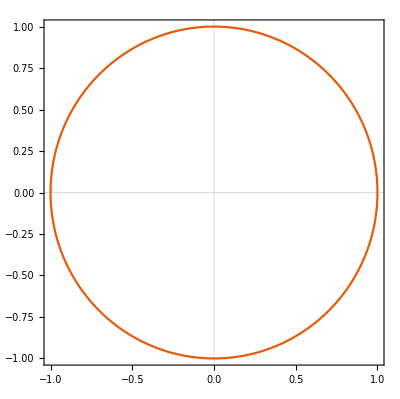

```mathematica
ParametricPlot[{Cos[u],Sin[u]},{u,0,2*Pi},PlotTheme->"Scientific"]
```

Notice that the first argument is a set of functions enclosed in braces - these are the x and y coordinates of the curve. The second argument is the domain of definition. We can combine this with the Manipulate function, and use a slider to change how much of the curve we plot as follows:

```mathematica
Manipulate[ParametricPlot[{Cos[u],Sin[u]},{u,0,c},PlotTheme->"Scientific",PlotRange->{{-2,2},{-2,2}}],{c,0.01,2*Pi,Appearance->"Labeled"}]
```

Notice that we use ParametricPlot with an interval from 0 to c, and then in the Manipulate function we define c from 0.01 to 2π. If we try to start c from 0 then the ParametricPlot fails because the interval starts at 0 and ends at 0. We also use a fixed plotting range otherwise it is updated dynamically.

Sometimes, it is useful to “watch” the curve being drawn. This can be accomplished in Mathematica by replacing Manipulate with the Animate function:

```mathematica
Animate[ParametricPlot[{Cos[u],Sin[u]},{u,0,c},PlotRange->{{-2,2},{-2,2}},PlotTheme->"Scientific"],{c,0.01,2*Pi,Appearance->"Labeled"}]
```

As u increases from 0 to 2π, the circle is traced out in a counter-clockwise direction. The interpretation of u in this case is straight-forward - it is the angle from the x-axis to the current point on the circle. 

How do we “know” that these parametric equations trace out a circle, and not just a curve that looks like a circle? Let’s check by substituting the definition of x and y into the equation for a circle of radius 1, centered at the origin, 
					x^2+y^2 = 1
					x^2+y^2 = cos^2(u) + sin^2(u) = 1
which is true if we recall a trigonometric identity cos^2(u) + sin^2(u) = 1. We can, of course, use Mathematica to do this work for us. Notice that we need to use the Simplify function to complete the process.

```mathematica
Cos[u]^2 + Sin[u]^2
Simplify[%]
```

Cos[u]^2+Sin[u]^2

## Exercises

Use the internet to find a set of parametric equations that define an ellipse, and use ParametricPlot and Manipulate to verify them visually. Show that the parametric equations satisfy the implicit equation for an ellipse. What is the interpretation of the parameter u in this case?

This is a small change to the parametric equations for a circle, and finding parametric equations on the internet should be straight-forward - try searching on “parametric equations for ellipse” or start with the Wikipedia page on conic section or ellipse.

```mathematica
Manipulate[ParametricPlot[{2*Cos[u],1*Sin[u]},{u,0,c},PlotTheme->"Scientific",PlotRange->{{-2,2},{-2,2}}],{c,0.01,2*Pi,Appearance->"Labeled"}]
```

Each value of u defines a point with the values 2* Cos(u) and 1*Sin(u)

A logarithmic spiral can be defined by the parametric equations
x = a e^(-b u) cos(u), y = a e^(-b u) sin(u), a>0, b >0, u ≥ 0
Use ParametricPlot and Manipulate to visualize the curve for different values of a and b. Use Limit to determine what happens as u → ∞? Interpret the variables a and b, and the parameter u.

This question involves a curve that has been of interest to mathematicians and scientists for many centuries. The parametric equations involve an unbounded domain which is an interesting case to consider. Try searching on the internet for the term “logarithmic spiral”.

```mathematica
Manipulate[ParametricPlot[{a E^(-b u)*Cos[u], a E^(-b u)*Sin[u]},{u,0,c},PlotTheme->"Scientific",PlotRange->{{-2,2},{-2,2}}],{c,0.01,2*Pi,Appearance->"Labeled"}, {a,0.01,2,Appearance->"Labeled"}, {b,0.01,2,Appearance->"Labeled"}]
```

A helix in 3D can be defined by the parametric equation

x = a cos(u), y = a sin(u), z = b u, a > 0, b > 0, u > 0

Use ParametricPlot3D and Manipulate to visualize this curve for different values of a and b. Interpret the variables a and b, and the parameter u.

This question demonstrates that it is relatively simple to define a curve in 3D - just define the x, y, and z coordinates in terms of a single parameter. This curve is a good example, and has been widely studied in modern biology given its connection to the shape of DNA. Use the Wikipedia article on “helix” as a starting point.

```mathematica
Manipulate[ParametricPlot3D[{a*Cos[u],a*Sin[u], b*u}, {u,0,c},PlotTheme->"Scientific",PlotRange->{{-2,2},{-2,2}}],{c,0.01,2*Pi,Appearance->"Labeled"}, {a,0.01,2,Appearance->"Labeled"}, {b,0.01,2,Appearance->"Labeled"}]
```

Find an interesting parametric curve, and implement it in Mathematica. Interpret the parameter and any variables.

There are lots of fun curves out there!

```mathematica
Manipulate[ParametricPlot[{(a+b)*Cos[u]−c*Cos[(a/b+u)*u],(a+b)*Sin[u]−c*Sin[(a/b+1)*u]},{u,0,c},PlotTheme->"Scientific",PlotRange->{{-20,20},{-20,20}}],{c,0.01,2*Pi,Appearance->"Labeled"}, {a,0.01,2,Appearance->"Labeled"}, {b,0.01,2,Appearance->"Labeled"}]
```

## 1.4 Data-driven Curves

We are often tasked with finding a curve that fits a set of data. You’ve probably seen informal approaches to this, particularly when finding the best-fit straight-line to a set of data points. We could take such an informal approach, and use Manipulate to tune a curve until the fit to the data “looks” good. Let’s start with some data:

{{0,1},{1,0},{3,2},{5,4}}

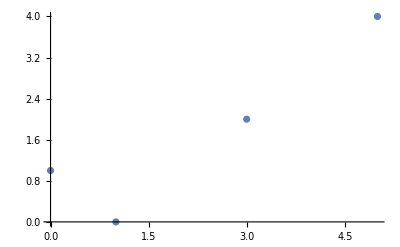

```mathematica
data = {{0,1},{1,0},{3,2},{5,4}}
ListPlot[data]
```

Notice that we’ve defined four points using the {{}} notation, and we’ve used ListPlot to plot these individual data points. Now let’s define a general straight-line and use Manipulate to find a decent fit:

```mathematica
data = {{0,1},{1,0},{3,2},{5,4}}
Manipulate[Show[ListPlot[data],Plot[m*t+b,{t,0,5},PlotRange->{{0,5},{0,5}}]],{m,0,5,Appearance->"Labeled"},{b,-2,2,Appearance->"Labeled"}]
```

{{0,1},{1,0},{3,2},{5,4}}

What makes a good fit? If you play with the parameters a little you will find that you are naturally drawn to lines that “thread” the data - some of the points are above and some of the points are below. Try m close to 0.7 and b close to 0.2.

The most common algorithms for determining the best fit seek to minimize the total vertical separation between the curve and the points - we will learn more about this later in the semester. For now, we will use FindFit which will do this for us automatically, especially if we provide starting guesses for the best parameter values. Here is how we use FindFit to determine the best-fit straight line:

b+m t

{m→0.694915,b→0.186441}

0.186441+0.694915 t

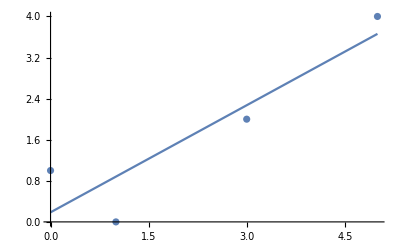

```mathematica
line = m*t+b
params = FindFit[data,line,{{m,0.7},{b,0.2}},t]
bestline = line/.params
Show[ListPlot[data],Plot[bestline,{t,0,5},PlotRange->{{0,5},{0,5}}]]
```

We’ve taken a very deliberate approach here of first defining the general equation for a line (in slope-intercept form). The first argument to FindFit is the data, the second argument is the equation, the third argument is the parameters (with a guess for each), and the last argument is the independent variable. The output is a list of assignments which define the parameter values that give the best fit. We end by substituting the best-fit parameters into the general equation for a line in order to define the best-fit line equation, and then we plot both the line and the data to visually check.

Let’s try fitting a parabola instead. We first need to decide what form of equation for a parabola we should use. We saw earlier that the vertex-form is often easier to interpret graphically, so let’s try that and we will use Manipulate to determine reasonable guesses for the parameters.

```mathematica
Manipulate[Show[ListPlot[data],Plot[g*(t-h)^2+k,{t,0,5},PlotRange->{{0,5},{0,5}}]],{g,0,2,Appearance->"Labeled"},{h,0,2,Appearance->"Labeled"},{k,0,1,Appearance->"Labeled"}]
```

Now that we’ve used Manipulate to determine some good guesses for the parameters, we can go ahead and seek the best-fit solution.

k+g (-h+t)^2

{g→0.190955,h→0.697368,k→0.585526}

0.585526+0.190955 (-0.697368+t)^2

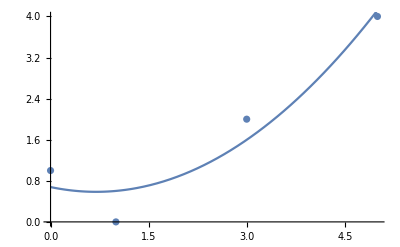

```mathematica
parab = g(t-h)^2+k
params = FindFit[data,parab,{{g,0.3},{h,1.1},{k,0.2}},t]
bestparab = parab/.params
Show[ListPlot[data],Plot[bestparab,{t,0,5},PlotRange->{{0,5},{0,5}}]]
```

Notice that we’ve just lightly edited the earlier code. We defined a general equation for a parabola in vertex-form, and then asked FindFit to determine the best parameters. Notice that they are slightly different than our guesses - this makes sense because we just used Manipulate to “eye-ball” a reasonable fit. This approach is very powerful - we can literally send FindFit it any function and have it find the best-fit, as long as we have reasonable guesses for the parameters. Let's try with an exponential function to complete this exploration.

```mathematica
Manipulate[Show[ListPlot[data],Plot[A*Exp[k*t],{t,0,5},PlotRange->{{0,5},{0,5}}]],{A,0,2,Appearance->"Labeled"},{k,0,1,Appearance->"Labeled"}]
```

A ⅇ^(k t)

{{A,0.4},{k,0.4}}

{A→0.483476,k→0.424726}

0.483476 ⅇ^(0.424726 t)

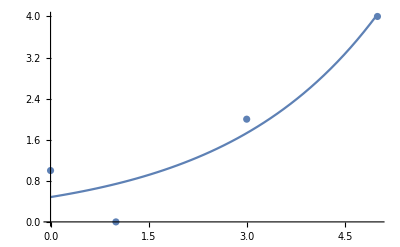

```mathematica
curve = A*Exp[k*t]
params = {{A,0.4},{k,0.4}}
bestparams = FindFit[data,curve,params,t]
bestcurve = curve/.bestparams
Show[ListPlot[data],Plot[bestcurve,{t,0,5},PlotRange->{{0,5},{0,5}}]]
```

Notice that we’ve taken some steps here to generalize our approach. We’ve defined a general curve and its associated parameters - we then use FindFit to find the best parameters, which we use to evaluate the best curve. We can now find the best-fit using any explicit curve we like.

## Exercises

Consider the following set of data, which is the US population from 1790 to 2010. The data is taken from national census data, with 1790 data labeled as year 0 and 2010 data labeled as year 220. The population numbers are in millions.

Find the best-fit exponential function of the form P(t) = 3.929214 e^(k t). According to this model, what is the growth rate of the US population? What is the predicted population in 2050? You should use Manipulate to find a good guess for the parameter value.

```mathematica
Manipulate[Show[ListPlot[pop],Plot[3.929214*Exp[k*t],{t,0,300},PlotRange->{{0,50},{0,300}}]],{k,0.02,0.03,Appearance->"Labeled"}]
```

Growth Rate of US population: 0.02243 
Predicted population 2050: 1339.75 million

```mathematica
3.929214*Exp[0.02243*260]
```

1339.75

Find the best-fit parabolic function (in vertex-form) using Manipulate to find a good guess for the parameters. According to this model, what is the predicted population in 2050? Which model is better?

```mathematica
Manipulate[Show[ListPlot[pop],Plot[g*(t-h)^2+k,{t,0,300},PlotRange->{{0,50},{0,300}}]],{g,0,0.01,Appearance->"Labeled"},{h,0,20,Appearance->"Labeled"},{k,0,20,Appearance->"Labeled"}]
```

```mathematica
0.00628(260)^2+0.95
```

425.478

Predicted population in 2050: 425.478 million people
The parabolic model is better

At this point we can simply look at the data and the best-fit and draw our own conclusions about how good the fit is. If you have experience with statistics and are interested in exploring this further, you can determine the "R Squared" value for each fit, which gives a quantitative measurement for the goodness of fit. In order to do this, you will need to use the function NonlinearModelFit and figure out how to extract this kind of information. If you are interested in a historical analysis of the US population, check out the following paper by Pearl and Reed from 1920 in which they use a logistic function.

```mathematica
pop = {{0,3.929214},{10,5.308483},{20,7.239881},{30,9.638453},{40,12.866020},{50,17.069453},{60,23.191876},{70,31.443321},{80,39.818449},{90,50.155783},{100,62.947714},{110,75.994575},{120,91.972266},{130,105.710620},{140,122.775046},{150,131.669275},{160,150.697361},{170,179.323175},{180,203.302031},{190,226.545805},{200,248.709873},{210,281.421906},{220,308.745538}}
```

{{0,3.92921},{10,5.30848},{20,7.23988},{30,9.63845},{40,12.866},{50,17.0695},{60,23.1919},{70,31.4433},{80,39.8184},{90,50.1558},{100,62.9477},{110,75.9946},{120,91.9723},{130,105.711},{140,122.775},{150,131.669},{160,150.697},{170,179.323},{180,203.302},{190,226.546},{200,248.71},{210,281.422},{220,308.746}}

PEPPER IS A FRUIT

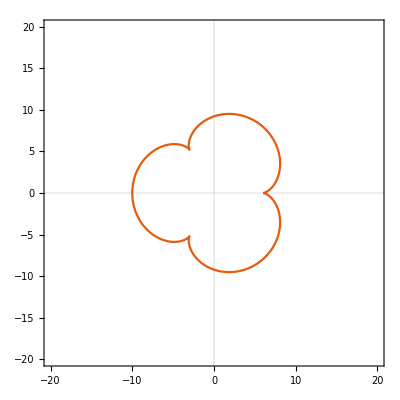

```mathematica
ParametricPlot[{2*(4*Cos[u]−Cos[4*u]),2*(4*Sin[u]−Sin[4*u])},{u,0,6.28319},PlotTheme->"Scientific",PlotRange->{{-20,20},{-20,20}}]
```